ComputationalPhysics-2Assignment-2.
Name:Md.MamunHossainNahid
RegNo:2017132008
HerewewillsolvetheSHOequation(d^2 x)/dt^2=-k/ωx(t)using4thorderRunge-Kuttamethodforinitialconditions:t=0
x(0)=1
ⅆx/ⅆt(0)=0
k/ω=1

The position at time 100. is 0.862097 .

The velocity at time 100. is 0.506227 .

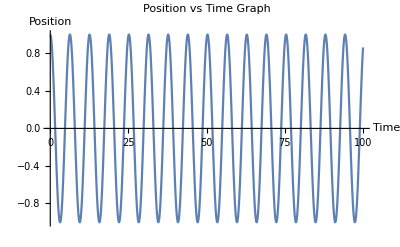

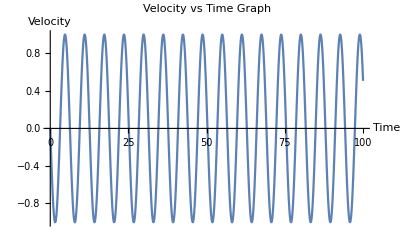

```mathematica
f1[t_,x_,v_]:= v;
f2[t_,x_,v_]:=-x;
UpperLimit=100;
LowerLimit=0;
h=0.05;
n=IntegerPart[(UpperLimit-LowerLimit)/h];


t=ConstantArray[0,n+1];
x=ConstantArray[0,n+1];
x⟦1⟧=1;

v=ConstantArray[0,n+1];

For[i=1, i≤n, i++,
{
k1= h*f1[t⟦i⟧,x⟦i⟧,v⟦i⟧];
l1=h*f2[t⟦i⟧,x⟦i⟧,v⟦i⟧];
k2=h*f1[t⟦i⟧+h/2,x⟦i⟧+k1/2,v⟦i⟧+l1/2];
l2=h*f2[t⟦i⟧+h/2,x⟦i⟧+k1/2,v⟦i⟧+l1/2];
k3= h*f1[t⟦i⟧+h/2,x⟦i⟧+k2/2,v⟦i⟧+l2/2];
l3=h*f2[t⟦i⟧+h/2,x⟦i⟧+k2/2,v⟦i⟧+l2/2];
k4= h*f1[t⟦i⟧+h,x⟦i⟧+k3,v⟦i⟧+l3];
l4= h*f2[t⟦i⟧+h,x⟦i⟧+k2,v⟦i⟧+l2];


t⟦i+1⟧=t⟦i⟧+h;
x⟦i+1⟧=x⟦i⟧+1/6*(k1+2*k2+2*k3+k4);
v⟦i+1⟧=v⟦i⟧+1/6*(l1+2*l2+2*l3+l4);
}
]
PositionVsTime=Thread[{t,x}];
VelocityVsTime=Thread[{t,v}];

StringForm["Position at time `` is `` ." , ToString[t⟦i⟧], ToString[x⟦i⟧]]
StringForm["Velocity at time `` is `` ." , ToString[t⟦i⟧], ToString[v⟦i⟧]]
ListLinePlot[PositionVsTime,AxesLabel->{"Time","Position"},PlotLabel->"Position vs Time Graph"]
ListLinePlot[VelocityVsTime, AxesLabel->{"Time","Velocity"},PlotLabel->"Velocity vs Time Graph"]
```